This notebook calculates and plots the limit circle picture of neutrino oscillations.

```mathematica
thetav=Pi/6
omegav=1
```

π/6

1

```mathematica
hamil=omegav{-Sin[2thetav],0,Cos[2thetav]}
```

{-(√3)/2,0,1/2}

```mathematica
sdot[s_]:=Cross[hamil,s]
```

```mathematica
Table[
{Norm@{s1,1,1},Norm@sdot[{s1,1,1}]},{s1,0,10}
]
```

{{√2,(√7)/2},{√3,√(1+(1/2+(√3)/2)^2)},{√6,√(1+(1+(√3)/2)^2)},{√11,√(1+(3/2+(√3)/2)^2)},{3 √2,√(1+(2+(√3)/2)^2)},{3 √3,√(1+(5/2+(√3)/2)^2)},{√38,√(1+(3+(√3)/2)^2)},{√51,√(1+(7/2+(√3)/2)^2)},{√66,√(1+(4+(√3)/2)^2)},{√83,√(1+(9/2+(√3)/2)^2)},{√102,√(1+(5+(√3)/2)^2)}}

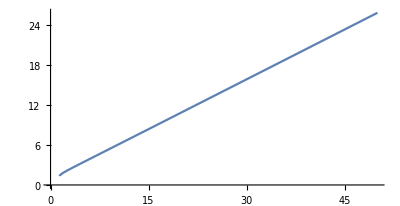

```mathematica
ParametricPlot[{Norm@{s1,1,1},Norm@sdot[{s1,1,1}]},{s1,0,50}]
```

```mathematica
VectorPlot3D[sdot[{s1,s2,s3}],{s1,-1,1},{s2,-1,1},{s3,-1,1},VectorColorFunction->"Rainbow",PlotLabel->"Flavor Isospin and Derivative of It",ViewPoint->{0,Infinity,0}]
```

-Graphics3D-